# Basic functions and definitions

## Basic Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Quiet[Needs["ErrorBarPlots`"]]
```

```mathematica
pr[list_,c_]:=Table[list⟦i⟧⟦c⟧,{i,1,Length[list]}]
```

```mathematica
resolution={1024,1024};
```

## Data Extraction Functions

### Get the average data from data in files

```mathematica
GetFileData[fileName_,fileType_]:=If[FileExistsQ[fileName<>"/number.csv"],({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,
data={},
name=fileName<>"/"<>fileType,
For[i=1,i≤num,++i,If[FileExistsQ[name<>ToString[i]<>".csv"],AppendTo[data,Import[name<>ToString[i]<>".csv"]],Null]],
Table[{data⟦1⟧⟦j⟧⟦1⟧,Sum[data⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[data]}]/Length[data]},{j,1,Length[data⟦1⟧]}]
})⟦5⟧,{}]
```

### Get the standard deviation of data

```mathematica
GetFileError[fileName_,fileType_]:=If[FileExistsQ[fileName<>"/number.csv"],({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,
data={},
name=fileName<>"/"<>fileType,
For[i=1,i≤num,++i,If[FileExistsQ[name<>ToString[i]<>".csv"],AppendTo[data,Import[name<>ToString[i]<>".csv"]],Null]],

ave=GetFileData[fileName,fileType],
Table[{data⟦1⟧⟦j⟧⟦1⟧,(Sum[(data⟦i⟧⟦j⟧⟦2⟧-ave⟦j⟧⟦2⟧)^2,{i,1,Length[data]}]/Length[data])^(1/2)},{j,1,Length[data⟦1⟧]}]
})⟦6⟧,{}]
```

### Create data for a ListErrorPlot

```mathematica
GetFileDataWithError[fileName_,fileType_]:=({
g1=GetFileData[fileName,fileType];,
g2=GetFileError[fileName,fileType];,
Partition[Riffle[pr[g1,2],pr[g2,2]],2]
})⟦3⟧
```

### Get good plot limits for list error plots

```mathematica
PlotLimits[dataErrorList_,rounding_]:=({
mn=Min[Table[dataErrorList⟦i⟧⟦1⟧-dataErrorList⟦i⟧⟦2⟧,{i,1,Length[dataErrorList]}]],
mx=Max[Table[dataErrorList⟦i⟧⟦1⟧+dataErrorList⟦i⟧⟦2⟧,{i,1,Length[dataErrorList]}]],
mn-rounding(mx-mn),
mx+rounding(mx-mn)
})⟦3;;4⟧
```

## Special error plotting functions

## For plotting (x,y) data with error strips

```mathematica
ClearAll[GetRange,plusMinusMean,Process,ListPlotSingleError,ListPlotError]
```

```mathematica
DefaultColors=Table[RandomColor[],{i,1,100}];
```

```mathematica
GetRange[data_,sigmas_]:=({
mn=Min[Table[Min[Table[data⟦i⟧⟦j⟧⟦2⟧-sigmas⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sigmas⟦i⟧]}]],{i,1,Length[data]}]],
mx=Max[Table[Max[Table[data⟦i⟧⟦j⟧⟦2⟧+sigmas⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sigmas⟦i⟧]}]],{i,1,Length[data]}]],
mn-0.05(mx-mn),
mx+0.05(mx-mn)
})⟦3;;4⟧
```

```mathematica
plusMinusMean[data_,sigma_]:=Transpose[Map[{#⟦1⟧+#⟦2⟧,#⟦1⟧-#⟦2⟧,#⟦1⟧}&,Transpose[{data,sigma}]]]
```

```mathematica
Process[data_,sigma_]:=MapThread[{#1,#2}&,{pr[data,1],#}]&/@plusMinusMean[pr[data,2],pr[sigma,2]]
```

```mathematica
Options[ListPlotSingleError]=Options[ListPlot];
ListPlotSingleError[data_,sigma_,range_:All,opts:OptionsPattern[]]:=
ListPlot[
Process[data,sigma],
Joined->True,
PlotStyle->{Opacity[0],Opacity[0],
If[Length[OptionValue[PlotStyle]]≥i,OptionValue[PlotStyle]⟦i⟧,DefaultColors⟦i⟧]
},
Filling->{1->{2}},
FillingStyle->Directive[Opacity[0.2],
If[Length[OptionValue[PlotStyle]]≥i,OptionValue[PlotStyle]⟦i⟧,DefaultColors⟦i⟧]],
PlotRange->range,
Evaluate[FilterRules[{opts}, Options[ListPlot]]]]
```

```mathematica
ListPlotError[data_,sigmas_,opts:OptionsPattern[]]:=Show[Table[ListPlotSingleError[data⟦i⟧,sigmas⟦i⟧,GetRange[data,sigmas],opts],{i,1,Length[data]}]]
```

# Handle Single File

```mathematica
Header="CFvsTau_num5000_frac0.5_vel1";
```

### Get data and errors

```mathematica
pcvt=GetFileData[Header,"PCF"];
pcvte=GetFileError[Header,"PCF"];
gcvt=GetFileData[Header,"GCF"];
gcvte=GetFileError[Header,"GCF"];
```

```mathematica
pdiff=GetFileData[Header,"PDiff"];
pdiffe=GetFileError[Header,"PDiff"];
gdiff=GetFileData[Header,"GDiff"];
gdiffe=GetFileError[Header,"GDiff"];
```

```mathematica
pdiffF=GetFileData[Header,"PDiffFactor"];
pdiffFe=GetFileError[Header,"PDiffFactor"];
gdiffF=GetFileData[Header,"GDiffFactor"];
gdiffFe=GetFileError[Header,"GDiffFactor"];
```

## Plots

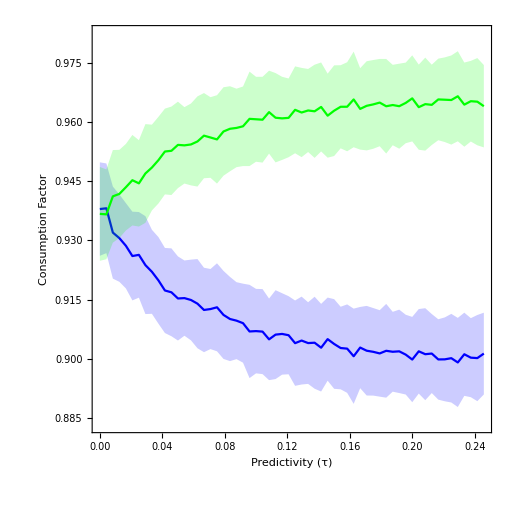

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pcvt,gcvt},{pcvte,gcvte},PlotStyle->{Blue,Green},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[
Framed[
Column[{
LineLegend[{Blue},     {"  Predictive"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pcvt,gcvt},{pcvte,gcvte},PlotStyle->{Blue,Green},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[
Framed[
Column[{
LineLegend[{Blue},     {"  Predictive"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.8,0.8}]]
(* End of the Legends *)
];
```

```mathematica
Export[Header<>"/CF.jpg",plot,"CompressionLevel"->0];
```

### Consumption factor difference

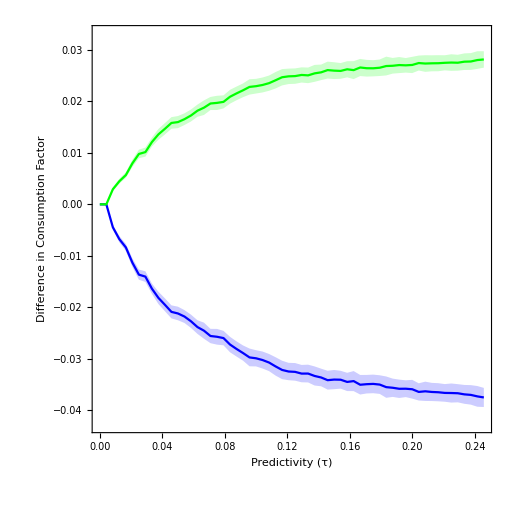

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdiff,gdiff},{pdiffe,gdiffe},PlotStyle->{Blue,Green},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Blue},     {"  Predictive"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},Background->White]
],Scaled[{0.8,0.45}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdiff,gdiff},{pdiffe,gdiffe},PlotStyle->{Blue,Green},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Blue},     {"  Predictive"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},Background->White]
],Scaled[{0.8,0.45}]]
(* End of the Legends *)
];
```

```mathematica
Export[Header<>"/Diff.jpg",plot,"CompressionLevel"->0];
```

### Plot consumption difference factor

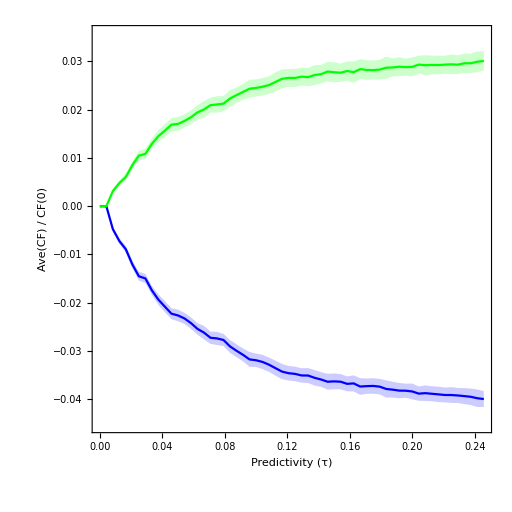

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdiffF,gdiffF},{pdiffFe,gdiffFe},PlotStyle->{Blue,Green},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Ave(CF) / CF(0)",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Blue},     {"  Predictive"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},Background->White]
],Scaled[{0.8,0.45}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdiffF,gdiffF},{pdiffFe,gdiffFe},PlotStyle->{Blue,Green},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Ave(CF) / CF(0)",labelFont,FontFamily->"Arial",Black]},ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Blue},     {"  Predictive"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Gradient"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
},Background->White]
],Scaled[{0.8,0.45}]]
(* End of the Legends *)
];
```

```mathematica
Export[Header<>"/DiffFactor.jpg",plot,"CompressionLevel"->0];
```

# Get data from multiple files

#### Get data

```mathematica
pdt01=GetFileData["CFvsTau_num5000_frac0.01_vel1","PDiff"];
gdt01=GetFileData["CFvsTau_num5000_frac0.01_vel1","GDiff"];
pdt10=GetFileData["CFvsTau_num5000_frac0.1_vel1","PDiff"];
gdt10=GetFileData["CFvsTau_num5000_frac0.1_vel1","GDiff"];
pdt20=GetFileData["CFvsTau_num5000_frac0.2_vel1","PDiff"];
gdt20=GetFileData["CFvsTau_num5000_frac0.2_vel1","GDiff"];
pdt50=GetFileData["CFvsTau_num5000_frac0.5_vel1","PDiff"];
gdt50=GetFileData["CFvsTau_num5000_frac0.5_vel1","GDiff"];
```

#### Get error

```mathematica
pdt01e=GetFileError["CFvsTau_num5000_frac0.01_vel1","PDiff"];
gdt01e=GetFileError["CFvsTau_num5000_frac0.01_vel1","GDiff"];
pdt10e=GetFileError["CFvsTau_num5000_frac0.1_vel1","PDiff"];
gdt10e=GetFileError["CFvsTau_num5000_frac0.1_vel1","GDiff"];
pdt20e=GetFileError["CFvsTau_num5000_frac0.2_vel1","PDiff"];
gdt20e=GetFileError["CFvsTau_num5000_frac0.2_vel1","GDiff"];
pdt50e=GetFileError["CFvsTau_num5000_frac0.5_vel1","PDiff"];
gdt50e=GetFileError["CFvsTau_num5000_frac0.5_vel1","GDiff"];
```

## Plots

### Predictive

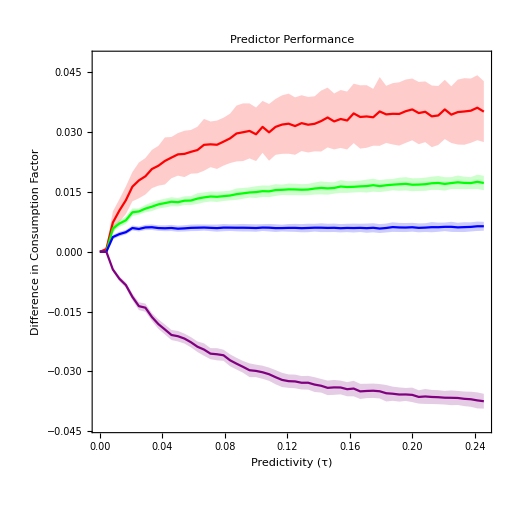

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{pdt01,pdt10,pdt20,pdt50},{pdt01e,pdt10e,pdt20e,pdt50e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictor Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive: 1%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive: 10%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive: 20%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive: 50%"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.8,0.32}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{pdt01,pdt10,pdt20,pdt50},{pdt01e,pdt10e,pdt20e,pdt50e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Predictor Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive: 1%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive: 10%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive: 20%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive: 50%"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.8,0.32}]]
(* End of the Legends *)
];
```

```mathematica
Export["CFvPred.jpg",plot,"CompressionLevel"->0];
```

### Gradient

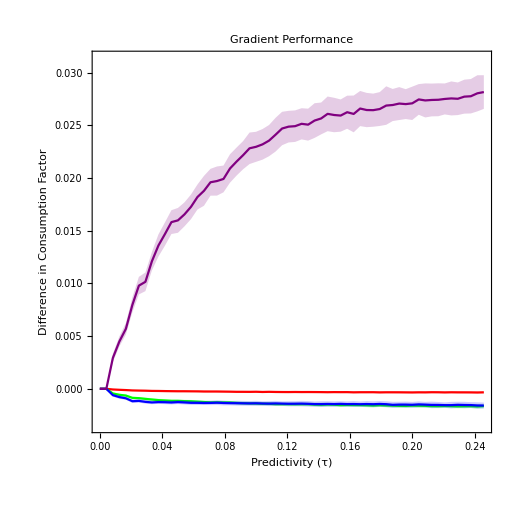

```mathematica
ratio=0.5;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
Show[
(* The plot *)
ListPlotError[{gdt01,gdt10,gdt20,gdt50},{gdt01e,gdt10e,gdt20e,gdt50e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Gradient Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive: 1%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive: 10%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive: 20%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive: 50%"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.8,0.32}]]
(* End of the Legends *)
]
```

```mathematica
ratio=1;
fontSize=20*ratio;
labelFont=24*ratio;
lineSize=50*ratio;
plot=Show[
(* The plot *)
ListPlotError[{gdt01,gdt10,gdt20,gdt50},{gdt01e,gdt10e,gdt20e,gdt50e},PlotStyle->{Red,Green,Blue,Purple},Frame->True,FrameTicksStyle->Directive[labelFont,Black],FrameLabel->{Style["Predictivity (τ)",labelFont,FontFamily->"Arial",Black],Style["Difference in Consumption Factor",labelFont,FontFamily->"Arial",Black]},PlotLabel->Style["Gradient Performance",FontSize->1.5labelFont,Black],ImageSize->ratio*resolution,AspectRatio->1],
(* The legend *)
Epilog->Inset[Framed[
Column[{
LineLegend[{Red},     {"  Predictive: 1%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Green},{"  Predictive: 10%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Blue},{"  Predictive: 20%"},LabelStyle->fontSize,LegendMarkerSize->lineSize],
LineLegend[{Purple},{"  Predictive: 50%"},LabelStyle->fontSize,LegendMarkerSize->lineSize]
}],Background->White
],Scaled[{0.8,0.32}]]
(* End of the Legends *)
];
```

```mathematica
Export["CFvPred-Grad.jpg",plot,"CompressionLevel"->0];
```